# PHYS 5013 HW 10

## Problem 2:

### Part a.)

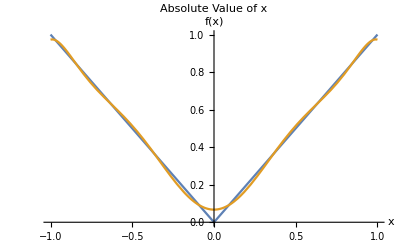

```mathematica
basis=Table[√((2 n+1)/2)LegendreP[n,x],{n,0,8}];
fxn=Abs[x];
coeffs=Integrate[fxn basis, {x,-1,1}];
appFxn = coeffs.basis;
Plot[{fxn,appFxn},{x,-1,1}, PlotLabel->"Absolute Value of x",AxesLabel->{x,f[x]}]
```

### Part b.)

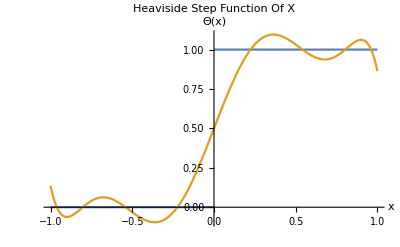

```mathematica
Clear["Global`*"];
basis=Table[√((2 n+1)/2)LegendreP[n,x],{n,0,8}];
fxn=HeavisideTheta[x];
coeffs=Integrate[fxn basis,{x,-1,1}];
appFxn=coeffs.basis;
Plot[{fxn,appFxn},{x,-1,1},PlotLabel->"Heaviside Step Function Of X",AxesLabel->{x,Θ[x]}]
```

## Problem 3:

```mathematica
ClearAll["Global`*"];
GramSchmidt =Orthogonalize[{1,x,x^2,x^3,x^4},Integrate[#1 #2 Exp[-x^2],{x,-Infinity,Infinity}]&]//Simplify;
GramSchmidtFxn = 1/π^(1/4)+(√2 x)/π^(1/4)+(√2 (-1/2+x^2))/π^(1/4)+(x (-3+2 x^2))/(√3 π^(1/4))+(3-12 x^2+4 x^4)/(2 √6 π^(1/4));
HermitePolyFxn=HermiteH[4,x];
Plot3D[{GramSchmidtFxn,HermitePolyFxn},{x,-3,3},{y,-10,10},PlotLabel->"Gram Shmidt Vs. Hermite Polynomials",AxesLabel->{x,z,F[x]},PlotLegends->{"Hermite Polynomials","Gram Schmidt"}]
```

-Graphics3D-

## Problem 4:

### Part a.)

```mathematica
ClearAll["Global`*"];
fxn=Piecewise[{{-1,x<0},{0,x==0},{1,x>0}}];
an=1/Pi*Integrate[fxn*Cos[n x],{x,-Pi,Pi}]
```

0

```mathematica
bn=1/Pi*Integrate[fxn*Sin[n x],{x,-Pi,Pi}]
```

-(2 (-1+Cos[n π]))/(n π)

```mathematica
ClearAll["Global`*"];
fxn=Abs[x]/(Pi);
an=1/Pi*Integrate[fxn * Cos[n x],{x,-Pi,Pi}]
```

(2 (-1+Cos[n π]+n π Sin[n π]))/(n^2 π^2)

```mathematica
bn=1/Pi*Integrate[fxn*Sin[n x],{x,-Pi,Pi}]
```

0

### Part b.)

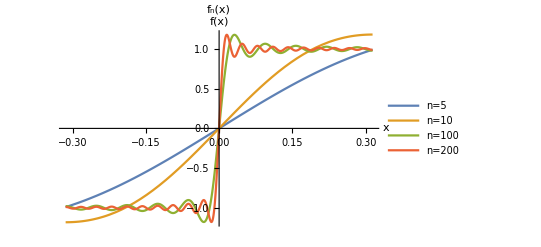

```mathematica
ClearAll["Global`*"];
fxn=Piecewise[{{-1,x<0},{0,x==0},{1,x>0}}];
a0=1/Pi*Integrate[fxn ,{x,-Pi,Pi}];
an=1/Pi*Integrate[fxn * Cos[n x],{x,-Pi,Pi}];
bn=1/Pi*Integrate[fxn*Sin[n x],{x,-Pi,Pi}];
fxn5=Total[Table[an Cos[n x]+bn Sin[n x],{n,1,5}]];
fxn10=Total[Table[an Cos[n x]+bn Sin[n x],{n,1,10}]];
fxn100=Total[Table[an Cos[n x]+bn Sin[n x],{n,1,100}]];
fxn200=Total[Table[an Cos[n x]+bn Sin[n x],{n,1,200}]];
Plot[{fxn5,fxn10,fxn100,fxn200},{x,-Pi/10,Pi/10},PlotLabel->Subscript[f,n][x],AxesLabel->{x,f[x]},PlotLegends->{"n=5","n=10","n=100","n=200"}]
```

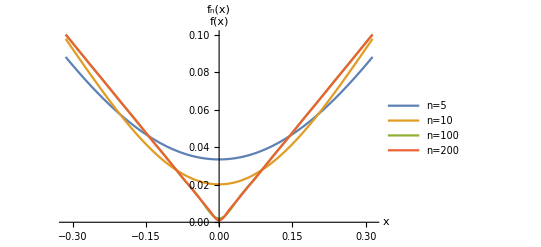

```mathematica
ClearAll["Global`*"];
fxn=Abs[x]/(Pi);
a0=1/Pi*Integrate[fxn ,{x,-Pi,Pi}];
an=1/Pi*Integrate[fxn * Cos[n x],{x,-Pi,Pi}];
bn=1/Pi*Integrate[fxn*Sin[n x],{x,-Pi,Pi}];
fxn5=a0/2+Total[Table[an Cos[n x]+bn Sin[n x],{n,1,5}]];
fxn10=a0/2+Total[Table[an Cos[n x]+bn Sin[n x],{n,1,10}]];
fxn100=a0/2+Total[Table[an Cos[n x]+bn Sin[n x],{n,1,100}]];
fxn200=a0/2+Total[Table[an Cos[n x]+bn Sin[n x],{n,1,200}]];
Plot[{fxn5,fxn10,fxn100,fxn200},{x,-Pi/10,Pi/10},PlotLabel->Subscript[f,n][x],AxesLabel->{x,f[x]},PlotLegends->{"n=5","n=10","n=100","n=200"}]
```

## Problem 6:

### Part c.)

```mathematica
ClearAll["Global`*"];
psi[n_,s_]=√2 *Sin[n Pi s];
FirstOrder = Refine[Integrate[psi[n,s]*δ s*psi[n,s],{s,0,1}],Element[n,Integers]]
```

δ/2

### Part d.)

```mathematica
SecondOrder =N[Total[Table[If[m≠1,(Integrate[√2 Sin[m Pi s]*δ s*√2 Sin[Pi s],{s,0,1}])^2/(Pi^2-m^2 Pi^2),0],{m,0,10}]]]
```

-0.00109726 δ^2